```mathematica
SetDirectory["/Users/tanjona/Documents/asa/projects/Perrotti_spore_count"]
```

/Users/tanjona/Documents/asa/projects/Perrotti_spore_count

```mathematica
is = 200;
ps = {{Thick,LightGray},{Thick,Gray},{Thick,Black}};
(*ps3 = {{Gray, Thick, Dashed},{Gray, Thick},{Black, Thick},{Gray, Thick},{Gray, Thick, Dashed}, {Red, Thick}};*)
ps3 = {{Black, Thick},{LightGray, Thick},{LightGray, Thick},{Orange,Thick}};
ps4 = {{Black, Thick},{LightGray, Thick},{LightGray, Thick},{Orange,Thick}};
ls = Directive[12,Black];
gs = Directive[Gray, Thick,Dashed];
gs1 = {{{Directive[LightGray, Thick,Dashed],Directive[Gray, Thick,Dashed],Directive[Black, Thick,Dashed]}},None};
```

```mathematica
lg1 = LineLegend[{LightGray,Gray,Black},{"0.1","0.5","0.9"},LegendLabel->"True proportion\nof tracers"]
```

```mathematica
lg2 = LineLegend[{LightGray,Gray,Black},{"20","100","500"},LegendLabel->"Total count (n)"]
```

```mathematica
(*
Compute the likelihood function  for a given sample size,number of tracers found, and tracers added
The maximum likelihood is scaled to one
*)
ComputeLikelihood[samplesize_, tracerfound_,traceradded_]:=Module[{res,temp,max, maxlik,pp,step},
If[samplesize == tracerfound, res = "NA";Goto["here"]];
pp = tracerfound/samplesize;
max = Ceiling[1/(pp (1- pp)) traceradded (1/pp - 1)];
step =Ceiling[ max/500];
maxlik  = PDF[HypergeometricDistribution[samplesize, traceradded,  Ceiling[traceradded samplesize/tracerfound ] ], tracerfound]//N;
temp = Table[{spore,PDF[HypergeometricDistribution[samplesize, traceradded,  Ceiling[traceradded+spore] ], tracerfound]/maxlik},{spore, 0,max,step}]//Quiet;
res = temp;
Label["here"];
res];

(* Find the 95% confidence interval for a p reduction in the maximum likelihood*)
ComputeCI[samplesize_, tracerfound_,traceradded_,NN_]:= Module[{res,pp = tracerfound/samplesize,accept = {}, dLik, fLik, ymax, bestestim ,xx,yy,dat},

(* Construct the continuous likelihood function *)
dLik = ComputeLikelihood[samplesize, tracerfound, traceradded]; 
If[dLik== "NA",res = {"NA", "NA","NA" , NN};Goto["here"]];
fLik = Interpolation[dLik];


(* generate random bivariate data *)
bestestim=traceradded(1/pp-1);
ymax = Floor[1/(pp (1- pp))bestestim ];
dat =Transpose[{RandomReal[{0,ymax},NN], RandomReal[{0,1.005},NN]}];

(* Rejection sampling*)
Do[
xx = dat[[i,1]];
yy = dat[[i,2]];
If[yy<= fLik[xx],AppendTo[accept,xx]]//Quiet;
,{i, Length@dat}];

res=  Flatten[{bestestim,Quantile[accept, {0.025,0.25,0.75,0.975}], Length@accept}];
Label["here"];
res];

(* Find the 95% confidence interval where number of tracers added is random *)
ComputeCI2[samplesize_, tracerfound_,tracerMean_, tracerSD_,NN_, rep_]:= Module[{randtracer,res,pp = tracerfound/samplesize,accept = {}, dLik, fLik, ymax, bestestim ,xx,yy,dat},

(* Sample for tracer added *)
randtracer = Ceiling[RandomReal[NormalDistribution[tracerMean,tracerSD], rep]];

If[samplesize== tracerfound,res = ConstantArray["NA",5];Goto["here"]];

Do[
(* Construct the continuous likelihood function *)
dLik = ComputeLikelihood[samplesize, tracerfound, randtracer[[k]]]; 

fLik = Interpolation[dLik];

(* generate random bivariate data *)
bestestim=randtracer[[k]](1/pp-1);
ymax = Floor[1/(pp (1- pp))bestestim ];
dat =Transpose[{RandomReal[{0,ymax},NN], RandomReal[{0,1.005},NN]}];

(* Rejection sampling*)
Do[
xx = dat[[i,1]];
yy = dat[[i,2]];
If[yy<= fLik[xx],AppendTo[accept,xx]]//Quiet;
,{i, Length@dat}];
,{k,rep}];

res= N@Flatten[{tracerMean(1/pp-1), Quantile[accept, {0.025,0.25,0.75,0.975}]}];
Label["here"];
res];

(* Generate data for the true density, either linear increase or abrupt change at mid interval *)
trueDensity[t0_,t1_,step_,d0_, d1_, abrupt_]:=Module[{res, time, temp, slope,l1,l2},
time = Range[t0,t1,step];
l1 = Ceiling[Length@time/2];
l2 = Length@time - l1 ;
If[abrupt == True,
temp =Flatten[ {ConstantArray[Ceiling@d0, l1],ConstantArray[Ceiling@d1,l2]}],
slope = (d1-d0)/(t1-t0);
temp = Ceiling[(time - t0) slope + d0]; 
];
res = Transpose[{time,temp}];
res];

axisFlip=#/. {x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;

Prob2[NS_,n_,NT_]:=Binomial[n,1] Binomial[NT +NS - n-1,NS-1]/Binomial[(NS + NT),NS]
```

## Figure 1

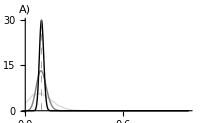

```mathematica
p1 = 0.1; NN = 5000/p1; 
dat1a = Table[N@Table[{nn/n,PDF[HypergeometricDistribution[n, Ceiling[p1 NN], Ceiling[NN] ],nn ]*n}, {nn, 0, n}],{n,{20,100,500}}]//Quiet;
fig1a = ListPlot[dat1a, Joined-> True,PlotRange->All,GridLines->{{p1},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "A)"},GridLinesStyle->gs]
```

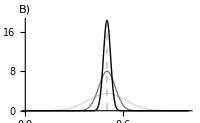

```mathematica
p2 = 0.5; NN = 5000/p2; 
dat1b = Table[N@Table[{nn/n,PDF[HypergeometricDistribution[n, Ceiling[p2 NN], Ceiling[NN] ],nn ]*n}, {nn, 0, n}],{n,{20,100,500}}]//Quiet;
fig1b = ListPlot[dat1b, Joined-> True,PlotRange->All,GridLines->{{p2},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "B)"},GridLinesStyle->gs]
```

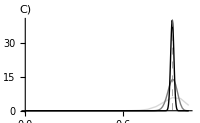

```mathematica
p3 = 0.9; NN = 1000/p3; 
dat1c = Table[N@Table[{nn/n,PDF[HypergeometricDistribution[n, Ceiling[p3 NN], Ceiling[NN] ],nn ]*n}, {nn, 0, n}],{n,{20,100,500}}]//Quiet;
fig1c = ListPlot[dat1c, Joined-> True,PlotRange->All,GridLines->{{p3},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "C)"},GridLinesStyle->gs]
```

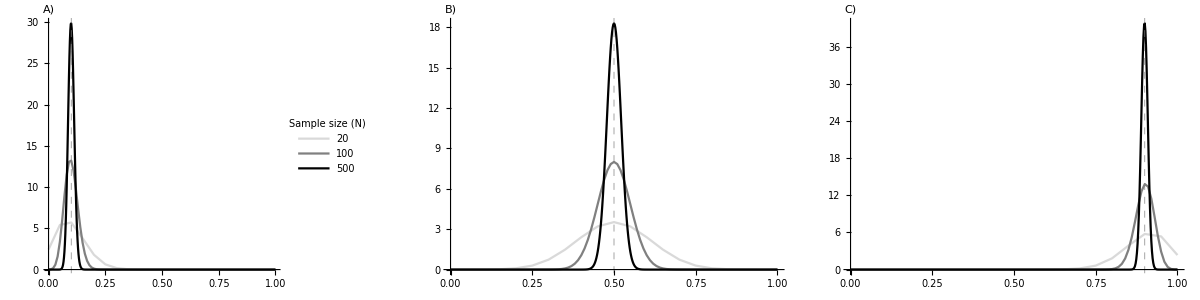
-Graphics-Frequency of tracersProbability

```mathematica
fig1 = Legended[Labeled[Grid[{{fig1a,fig1b,fig1c}}],Style[#, Black, 16,FontFamily->"Arial"] &/@{"Frequency of tracers", "Probability"}, {Bottom,Left}, RotateLabel->True],lg1]
```

```mathematica
Export["figs/fig1.pdf",fig1]
```

figs/fig1.pdf

## Figure 1 v2

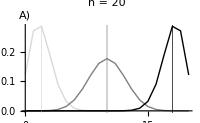

```mathematica
p1 = 0.1;p2 = 0.5;p3 = 0.9;
nsample1 = 20;
ntracers = 10000; 
dat1a = Table[N@Table[{nn,PDF[HypergeometricDistribution[nsample1, Ceiling[ntracers], Ceiling[ntracers/pp] ],nn ]}, {nn, 0, nsample1}],{pp,{p1,p2,p3}}]//Quiet;
fig1a = ListPlot[dat1a, Joined-> True,PlotRange->All,GridLines->{{{Ceiling[nsample1 p1], LightGray},{Ceiling[nsample1 p2],Gray},{Ceiling[nsample1 p3],Black}},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "A)"},GridLinesStyle->gs1, PlotLabel->"n = " <>ToString@nsample1]
```

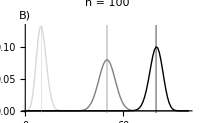

```mathematica
p1 = 0.1;p2 = 0.5;p3 = 0.8;
nsample2 = 100;
ntracers = 10000; 
dat1b = Table[N@Table[{nn,PDF[HypergeometricDistribution[nsample2, Ceiling[ntracers], Ceiling[ntracers/pp] ],nn ]}, {nn, 0, nsample2}],{pp,{p1,p2,p3}}]//Quiet;
fig1b = ListPlot[dat1b, Joined-> True,PlotRange->All,GridLines->{{{Ceiling[nsample2 p1], LightGray},{Ceiling[nsample2 p2],Gray},{Ceiling[nsample2 p3],Black}},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "B)"},GridLinesStyle->gs1, PlotLabel->"n = " <>ToString@nsample2]
```

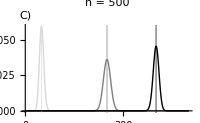

```mathematica
p1 = 0.1;p2 = 0.5;p3 = 0.8;
nsample3 = 500;
ntracers = 10000; 
dat1c = Table[N@Table[{nn,PDF[HypergeometricDistribution[nsample3, Ceiling[ntracers], Ceiling[ntracers/pp] ],nn ]}, {nn, 0, nsample3}],{pp,{p1,p2,p3}}]//Quiet;
fig1c = ListPlot[dat1c, Joined-> True,PlotRange->All,GridLines->{{{Ceiling[nsample3 p1], LightGray},{Ceiling[nsample3 p2],Gray},{Ceiling[nsample3 p3],Black}},None},ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "C)"},GridLinesStyle->gs1,  PlotLabel->"n = " <>ToString@nsample3]
```

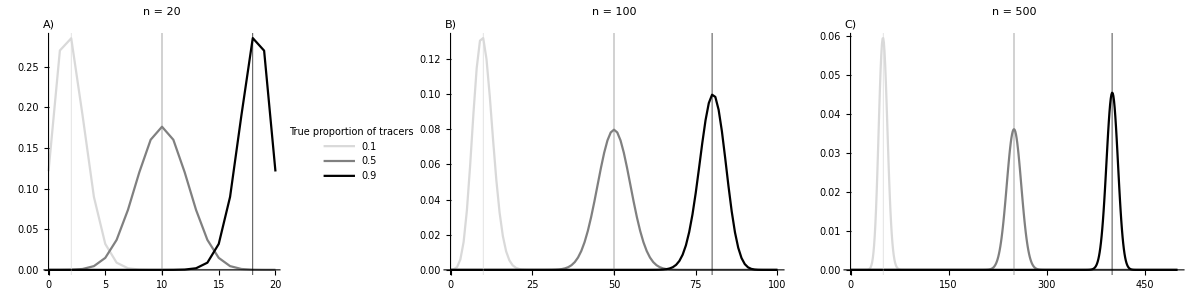
-Graphics-Number of tracers in the total countProbabilityTotal count

```mathematica
fig1 = Legended[Labeled[Grid[{{fig1a,fig1b,fig1c}}],Style[#, Black, 16,FontFamily->"Arial"] &/@{"Number of tracers in the total count", "Probability", "Total count"}, {Bottom,Left, Top}, RotateLabel->True],lg1]
```

```mathematica
Export["figs/fig1.pdf",fig1]
```

figs/fig1.pdf

## Figure 2

```mathematica
NT = 10000; 
n1 = 20 ; n2 = 100; n3 = 500;
p1 = 0.1; p2 = 0.5; p3 = 0.9;
```

```mathematica
dat2a1 = ComputeLikelihood[n1, Ceiling[p1 n1],NT];
dat2a2 = ComputeLikelihood[n2, Ceiling[p1 n2],NT];
dat2a3 = ComputeLikelihood[n3, Ceiling[p1 n3],NT];
```

```mathematica
dat2a1[[All,1]] /=1000;
dat2a2[[All,1]] /=1000;
dat2a3[[All,1]] /=1000;
```

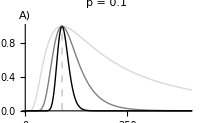

```mathematica
fig2a = ListPlot[{dat2a1,dat2a2,dat2a3},PlotRange->{{0,10^-3 4 NT/p1 },All},GridLines->{{Ceiling[10^-3 NT(1/p1 - 1)]}}, Joined->True,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "A)"},GridLinesStyle->gs, PlotLabel->"p = " <>ToString@p1]
```

```mathematica
dat2b1 = ComputeLikelihood[n1, Ceiling[p2 n1],NT];
dat2b2 = ComputeLikelihood[n2, Ceiling[p2 n2],NT];
dat2b3 = ComputeLikelihood[n3, Ceiling[p2 n3],NT];

dat2b1[[All,1]] /=1000;
dat2b2[[All,1]] /=1000;
dat2b3[[All,1]] /=1000;
```

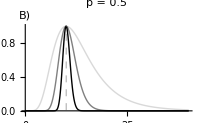

```mathematica
fig2b = ListPlot[{dat2b1,dat2b2,dat2b3},PlotRange->{{0,10^-3 2NT/p2},All},GridLines->{{Ceiling[10^-3 NT(1/p2 - 1)]}}, Joined->True,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "B)"},GridLinesStyle->gs, PlotLabel->"p = " <>ToString@p2]
```

```mathematica
dat2c1 = ComputeLikelihood[n1, Ceiling[p3 n1],NT];
dat2c2 = ComputeLikelihood[n2, Ceiling[p3 n2],NT];
dat2c3 = ComputeLikelihood[n3, Ceiling[p3 n3],NT];

dat2c1[[All,1]] /=1000;
dat2c2[[All,1]] /=1000;
dat2c3[[All,1]] /=1000;
```

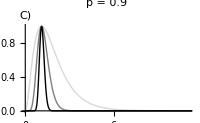

```mathematica
fig2c = ListPlot[{dat2c1,dat2c2,dat2c3},PlotRange->{{0,10^-3 NT/p3},All},GridLines->{{10^-3Ceiling[NT(1/p3 - 1)]}}, Joined->True,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "C)"},GridLinesStyle->gs, PlotLabel->"p = " <>ToString@p3]
```

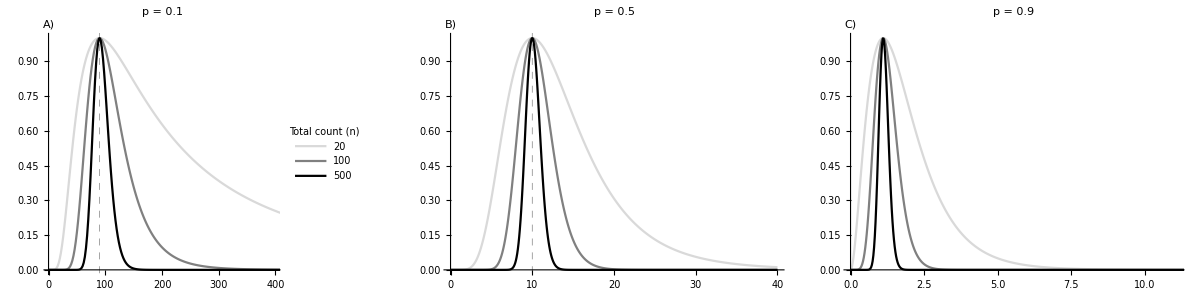
-Graphics-LikelihoodSpore density estimate (× 1000)

```mathematica
fig2 = Legended[Labeled[Grid[{{fig2a,fig2b,fig2c}}],Style[#, Black, 16,FontFamily->"Arial"] &/@{"Likelihood", "Spore density estimate (× 1000)"}, {Left,Bottom}, RotateLabel->True],lg2]
```

```mathematica
Export["figs/fig2.pdf",fig2]
```

figs/fig2.pdf

## Figure 3

```mathematica
nEnvelop = 10^5;
NT = 10000;
p1 = 0.1;
RES3a = {};
Do[
temp = ComputeCI[n,Ceiling[p1 n],NT, nEnvelop ];
res = {n, temp[[1]],temp[[2]],temp[[5]]}//Flatten;
AppendTo[RES3a,res];

,{n, PowerRange[10,640,2]}]
```

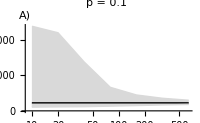

```mathematica
fig3a = ListLogLinearPlot[{RES3a[[All,{1,2}]],RES3a[[All,{1,3}]],RES3a[[All,{1,4}]]},Joined->True, PlotStyle->ps3,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "A)"},PlotRange->{All,{0,950000}}, AxesOrigin->{Automatic, 0},Filling->{1->{2},2->{3}},FillingStyle->LightGray, PlotLabel->"p = " <>ToString@p1]
```

```mathematica
nEnvelop = 10^5;
NT = 10000;
p2 = 0.5;
RES3b = {};
Do[
temp = ComputeCI[n,Ceiling[p2 n],NT, nEnvelop ];
res = {n, temp[[1]],temp[[2]],temp[[5]]}//Flatten;
AppendTo[RES3b,res];

,{n, PowerRange[10,640,2]}]
```

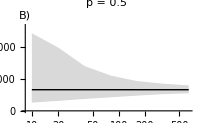

```mathematica
fig3b = ListLogLinearPlot[{RES3b[[All,{1,2}]],RES3b[[All,{1,3}]],RES3b[[All,{1,4}]]},Joined->True, PlotStyle->ps3,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "B)"},PlotRange->{Automatic,{0,40000}}, AxesOrigin->{Automatic, 0},Filling->{1->{2},2->{3}},FillingStyle->LightGray, PlotLabel->"p = " <>ToString@p2]
```

```mathematica
nEnvelop = 10^5;
NT = 10000;
p3 = 0.9;
RES3c = {};
Do[
temp = ComputeCI[n,Ceiling[p3 n],NT, nEnvelop ];
res = {n,temp[[1]],temp[[2]],temp[[5]]}//Flatten;
AppendTo[RES3c,res];

,{n, PowerRange[10,640,2]}]
```

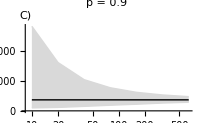

```mathematica
fig3c = ListLogLinearPlot[{RES3c[[All,{1,2}]],RES3c[[All,{1,3}]],RES3c[[All,{1,4}]]},Joined->True, PlotStyle->ps3,ImageSize->is, PlotStyle->ps, LabelStyle->ls, AxesLabel->{None, "C)"},PlotRange->{All,{0,All}}, AxesOrigin->{Automatic, 0},Filling->{1->{2},2->{3}},FillingStyle->LightGray, PlotLabel->"p = " <>ToString@p3]
```

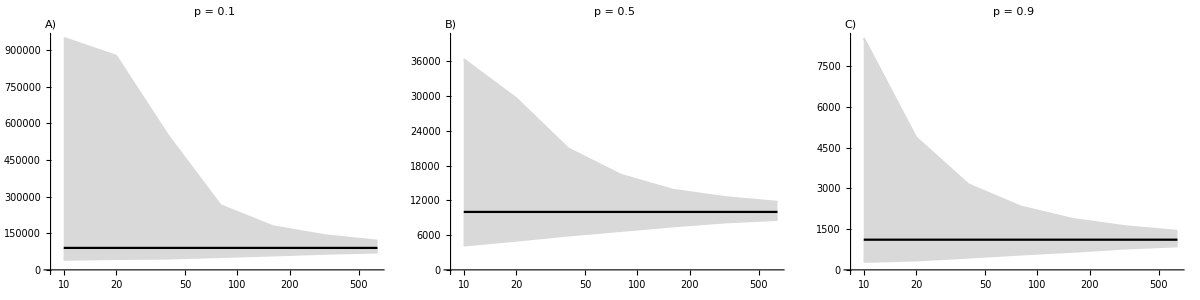
-Graphics-Total countCFS concentration

```mathematica
fig3 = Labeled[Grid[{{fig3a,fig3b,fig3c}}],Style[#, Black, 16,FontFamily->"Arial"] &/@{"Total count", "CFS concentration"}, {Bottom,Left}, RotateLabel->True]
```

```mathematica
Export["figs/fig3.pdf",fig3]
```

figs/fig3.pdf

## Figure 4

```mathematica
trueCount = Import["/Users/tanjona/Documents/asa/projects/Perrotti_spore_count/data/SporeCountExamples.xlsx"];
```

```mathematica
true1 = trueCount[[1,2;;,{1,2,3}]];
true2 = trueCount[[2,2;;,{1,2,3}]];
true3= trueCount[[3,2;;,{1,2,3}]];

trueNT1 = 18583;
trueNT2 = 18584;
trueNT3 = 12542;
sdNT = 500;
rep = 20;
NN =  5 10^4;
```

```mathematica
res1  =Table[N@Flatten@{true1[[i,1]],ComputeCI2[Ceiling@Total@true1[[i,{2,3}]], Ceiling@true1[[i,3]], trueNT1, sdNT,NN, rep]}, {i, Length@true1}];
res2  =Table[N@Flatten@{true2[[i,1]],ComputeCI2[Ceiling@Total@true2[[i,{2,3}]], Ceiling@true2[[i,3]], trueNT2, sdNT,NN, rep]}, {i, Length@true2}];
res3  =Table[N@Flatten@{true3[[i,1]],ComputeCI2[Ceiling@Total@true3[[i,{2,3}]], Ceiling@true3[[i,3]], trueNT3, sdNT,NN, rep]}, {i, Length@true3}];
```

```mathematica
padding = {{30,15},{30,30}};

fig4a = ListPlot[Reverse/@{res1[[All,{1,2}]],res1[[All,{1,3}]],res1[[All,{1,6}]]},Joined->True,PlotStyle->ps4,AxesOrigin->{1100,0} ,PlotRange->{{600,1100},{0,4000}},AxesLabel->{ None,"A)"},AspectRatio->0.25,ImageSize->3is,LabelStyle->ls,Filling->{1->{2},2->{3}},FillingStyle->LightGray,ImagePadding->padding,ScalingFunctions->{"Reverse", Automatic}, PlotLabel->Style["Appleman Lake",16,FontFamily->"Arial"]];
fig4b = ListPlot[Reverse/@{res2[[All,{1,2}]],res2[[All,{1,3}]],res2[[All,{1,6}]]},Joined->True,PlotStyle->ps4,AxesOrigin->{1100,0} ,PlotRange->{{600,1100},{0,4000}},AxesLabel->{ None,"B)"},AspectRatio->0.25,ImageSize->3is,LabelStyle->ls,Filling->{1->{2},2->{3}},FillingStyle->LightGray,ImagePadding->padding,ScalingFunctions->{"Reverse", Automatic}, PlotLabel->Style["Page-Ladson",16,FontFamily->"Arial"]];
fig4c = ListPlot[Reverse/@{res3[[All,{1,2}]],res3[[All,{1,3}]],res3[[All,{1,6}]]},Joined->True,PlotStyle->ps4,AxesOrigin->{500,0} ,PlotRange->{{60,500},{0,9000}},AxesLabel->{ None,"C)"},AspectRatio->0.25,ImageSize->3 is,LabelStyle->ls,Filling->{1->{2},2->{3}},FillingStyle->LightGray,ImagePadding->padding,ScalingFunctions->{"Reverse", Automatic}, PlotLabel->Style["Cupola Pond",16,FontFamily->"Arial"]];
```

```mathematica
axisFlip=#/. {x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
```

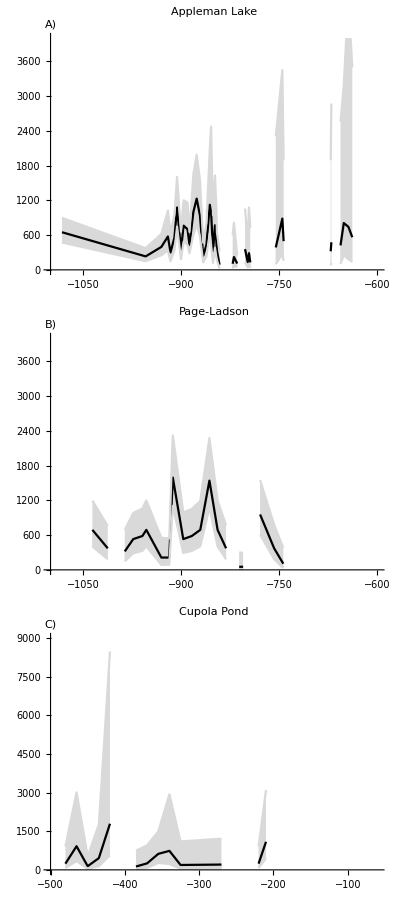
-Graphics-Estimated spore densityDepth (cm)

```mathematica
fig4= Labeled[Grid[{{fig4a,fig4b,fig4c}}//Transpose],Style[#, Black, 16,FontFamily->"Arial"] &/@{"Estimated spore density", "Depth (cm)"}, {Left,Bottom}, RotateLabel->True]
```

```mathematica
Export["figs/fig4.pdf",fig4]
```

figs/fig4.pdf

## Figure 5

```mathematica
(* Negative hypergeometric *)
Prob2[NS_,n_,NT_]:=Binomial[n,1] Binomial[NT +NS - n-1,NS-1]/Binomial[(NS + NT),NS]
```

```mathematica
cd = ColorData[2][#] & /@{1,3,6,9}
```

{RGBColor[0.8588235294117647, 0.00784313725490196, 0.00784313725490196],RGBColor[1., 0.4549019607843137, 0.2549019607843137],RGBColor[0.7019607843137254, 0.7450980392156863, 0.8235294117647058],RGBColor[0.33725490196078434, 0.403921568627451, 0.6235294117647059]}

```mathematica
lt = {Red,{Black,Dashed},{Black,AbsoluteThickness[1]},{Black,AbsoluteThickness[2 ]}};
ll = LineLegend[lt,Table[x,{x,{1,10,100,1000}}],LegendLabel->"Number of\nCFS in sample"]
```

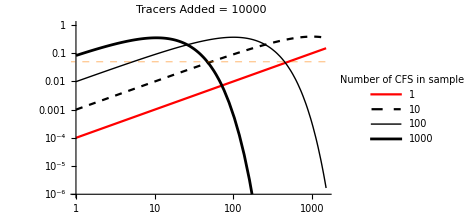
-Graphics-Probability of finding
the first CFSTotal count

```mathematica
NT = 10^4;NS= {1,10,100,1000};colL = cd;
lt = {Red,{Black,Dashed},{Black,AbsoluteThickness[1]},{Black,AbsoluteThickness[2 ]}};
Fig5 =
Legended[
Labeled[
Grid[{Table[
Show[
Table[Quiet@LogLogPlot[Prob2[NS[[i]],NN,NT],{NN,1,1500},PlotRange->{{1,1500},{0.000001,1}},PlotStyle->lt[[i]],ImagePadding->{{40,30},{20,20}},ImageSize->350,GridLines->{None,{{0.05,Directive[Orange,Dashed,AbsoluteThickness[1]]}}},LabelStyle->ls],{i,4}],
PlotLabel->Style["Tracers Added = " <> ToString@NT,16,FontFamily->"Helvetica", Black]],{NT,{10^4}}]}],Style[#,Black,16,FontFamily->"Helvetica"]&/@{"Probability of finding\nthe first CFS","Total count"},{Left,Bottom},RotateLabel->True],ll]
```

```mathematica
Export["figs/fig5.pdf",Fig5]
```

figs/fig5.pdf